## 1 - export of velocity only

```mathematica
SetDirectory["~/Documents/Processing/MIDIDance"];
data=Import["test1.txt","CSV"];
```

```mathematica
Dimensions@data
```

{210,9}

What fraction of hits was id. correctly?

```mathematica
nrSignals=6;
Total[If[#⟦2⟧==#⟦3⟧,1,0]&/@data]
(N@%)/(Length@data)
```

172

0.819048

What fraction of correct hits was there for each axis?

```mathematica
CorrectFraction[data_List]:=(N@Total[If[#⟦2⟧==#⟦3⟧,1,0]&/@data])/(Length@data);
```

```mathematica
CorrectFraction[Cases[data,{_,_,#,__}]]&/@Range[0,nrSignals-1]
```

{1.,1.,0.683544,0.793103,1.,1.}

How do the velocity values cluster?

```mathematica
ListPointPlot3D[Cases[data,{_,_,#,__}]⟦All,4;;6⟧&/@{0,1,2,-1},PlotRange->{{0,1},{0,1},{0,1}},AspectRatio->1,PlotStyle->{Red,Darker@Green,Blue,Black}]
```

-Graphics3D-

```mathematica
ListPointPlot3D[Cases[data,{_,#,2,__}]⟦All,4;;6⟧&/@{2,0,1},PlotRange->{{0,1},{0,1}},AspectRatio->1,PlotStyle->{Green,Red,Red,Black}]
```

## 2 - export of vector of past values

```mathematica
SetDirectory["~/Documents/Processing/MIDIDance"];
data=Import["test1-max.txt","CSV"];
```

```mathematica
(* detect the length of the vector of past values *)
nrSignals=6;
lengthSignals=(Length[First@data]-3)/nrSignals
```

3

```mathematica
(* separate data sets for different axis *)
xdatasep=({#⟦2;;3⟧,Partition[#⟦4;;-1⟧,lengthSignals]}&/@data);
```

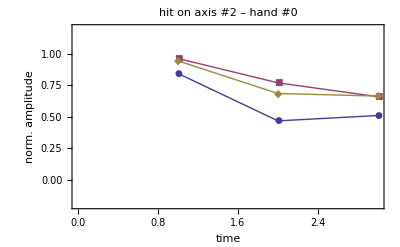

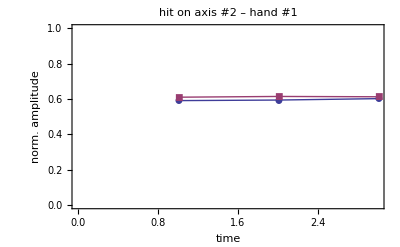

```mathematica
temp=Last@Transpose@Cases[xdatasep,{{_,axis=2},__}];
ListPlot[Mean[temp]⟦1;;3⟧,Joined->True,PlotMarkers->Automatic,FrameLabel->{"time","norm. amplitude"},PlotRange->{-0.2,1.2},PlotLabel->"hit on axis #"<>ToString@axis<>" – hand #0"]
ListPlot[Mean[temp]⟦4;;6⟧,Joined->True,PlotMarkers->Automatic,FrameLabel->{"time","norm. amplitude"},PlotRange->{0,1},PlotLabel->"hit on axis #"<>ToString@axis<>" – hand #1"]
```

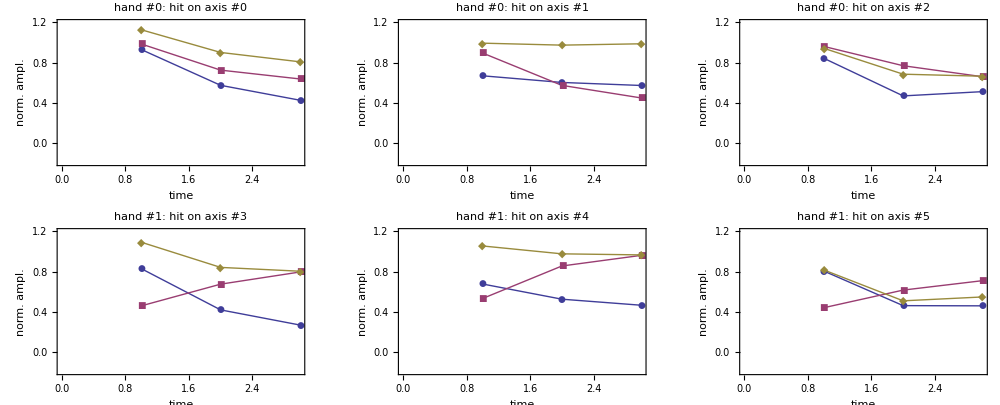

```mathematica
rangeOfHand={1;;3,4;;6};
GraphicsGrid[
Table[ListPlot[Mean[Last@Transpose@Cases[xdatasep,{{_,axisID+3*handID},__}]]⟦rangeOfHand⟦handID+1⟧⟧,Joined->True,PlotMarkers->Automatic,FrameLabel->{"time","norm. ampl."},PlotRange->{-0.2,1.2},PlotLabel->"hand #"<>ToString[handID]<>": hit on axis #"<>ToString[axisID+3*handID],ImageSize->200],{handID,0,1},{axisID,0,2}],
ImageSize->1000
]
```